1. Сформулировать в системе Mathematica заданную формулу f(t). Продолжить её периодически на всю числовую прямую.

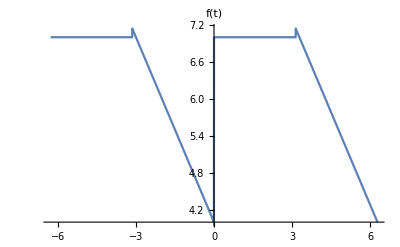

2. Построить апроксимацию f(t). Указать промежутки, где сумма ряда Фурье совпадает с f(t).

12.5708

12.5708

(11 π+π^2/2)/π

12.5708

-0.63662 | 0.909859
0. | 0.5
-0.0707355 | 0.303286
0. | 0.25
-0.0254648 | 0.181972
0. | 0.166667
-0.0129922 | 0.12998
0. | 0.125
-0.0078595 | 0.101095
0. | 0.1

Ряд Фурье для n = 2:

6.2854-0.63662 Cos[t]+0.909859 Sin[t]+0.5 Sin[2 t]

Ряд Фурье для n = 4:

6.2854-0.63662 Cos[t]-0.0707355 Cos[3 t]+0.909859 Sin[t]+0.5 Sin[2 t]+0.303286 Sin[3 t]+0.25 Sin[4 t]

Ряд Фурье для n = 7:

6.2854-0.63662 Cos[t]-0.0707355 Cos[3 t]-0.0254648 Cos[5 t]-0.0129922 Cos[7 t]+0.909859 Sin[t]+0.5 Sin[2 t]+0.303286 Sin[3 t]+0.25 Sin[4 t]+0.181972 Sin[5 t]+0.166667 Sin[6 t]+0.12998 Sin[7 t]

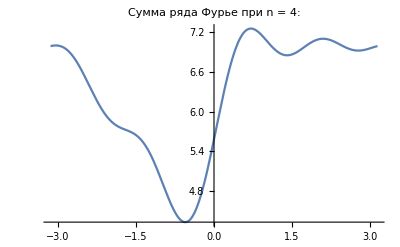

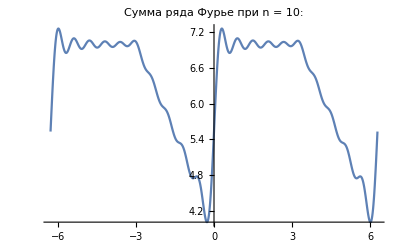

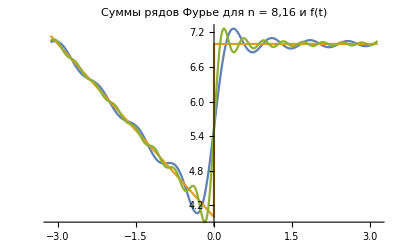

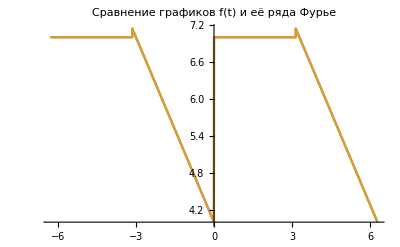

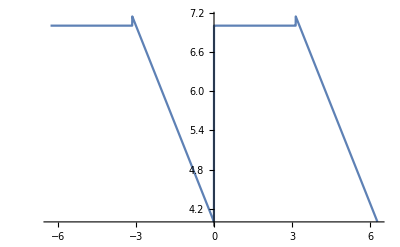

Сумма ряда фурье совпадает со значением f(t) на всём промежутке задания.

3. Найти значения суммы ряда фурье при различных значениях N. Объяснить полученный результат.

Сумма ряда Фурье для n = 3:

5.57804

Сумма ряда Фурье для n = 4:

5.57804

Сумма ряда Фурье для n = 7:

5.53959

Сумма ряда Фурье для n = 11:

5.53173

Сумма ряда Фурье для n = 18:

5.51767

Сумма ряда Фурье для n = 180:

5.50177

Сумма ряда Фурье для n = 18000:

5.50002

Значение функции f(t) в t = 0:

4

При увеличении N сумма ряда Фурье в точке t стремится к значению функции f в этой точке.

4. Нарисовать графики f(t), Sn(t), N = 8, 16.

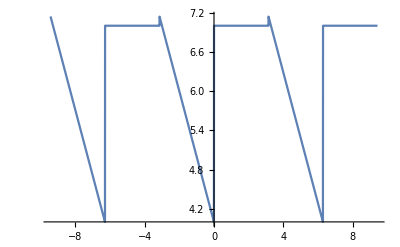

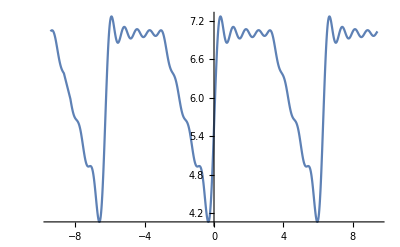

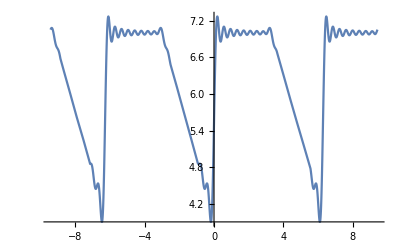

```mathematica
Clear[f]
Text["1. Сформулировать в системе Mathematica заданную формулу f(t). Продолжить её периодически на всю числовую прямую."]
f [t_]:=4-t /;-Pi≤t≤0
f[t_]:=7/;0<t≤Pi
f[t_]:=f[t-2*Pi]/;t>Pi
f[t_]:=f[t+2*Pi]/;t<-Pi
Plot[f[t],{t,-2*Pi,2*Pi},PlotLabel->"f(t)"]
Text["2. Построить апроксимацию f(t). Указать промежутки, где сумма ряда Фурье совпадает с f(t)."]
Clear[a,b,fs,L,ex,a1,b1,fourier]
L=Pi;
a[0]:=1/L*NIntegrate[f[t],{t,-L,L}];
a[0]
a[k_] := 1/L*NIntegrate[f[t]*Cos[k*Pi*t/L], {t, -L, L}];
b[k_] := 1/L*NIntegrate[f[t]*Sin[k*Pi*t/L], {t, -L, L}];
a1[0]:=1/L*(NIntegrate[4-t,{t,-Pi,0}]+NIntegrate[7,{t,0,Pi}]);
a1[0]
a1[0]:=1/L*(Integrate[4-t,{t,-Pi,0}]+Integrate[7,{t,0,Pi}]);
a1[0]
a1[0]:=N[11+Pi/2]
a1[0]
a1[k_]:=(8*Sin[k*Pi])/(k*Pi);
b1[k_]:=(2*Pi*k*Cos[Pi*k]-2*Sin[k*Pi])/(Pi*k^2)
a1[k_]:=N[((4+Pi)*k*Sin[k*Pi]+Cos[k*Pi]-1)/(Pi*k^2)+(7*Sin[k*Pi])/(k*Pi)]
b1[k_]:=N[(-4*k-Sin[k*Pi]+(4+Pi)*k*Cos[k*Pi])/(Pi*k^2)+(7-7*Cos[k*Pi])/(k*Pi)]
coeffs=Table[{a1[i],b1[i]},{i,1,10}];
TableForm[coeffs]
row[n_,t_]:=a1[0]/2+ Sum[a1[k]*Cos[k*Pi*t/L]+b1[k]*Sin[k*Pi*t/L],{k,1,n}];
Text["Ряд Фурье для n = 2: "]
row[2,t]
Text["Ряд Фурье для n = 4: "]
row[4,t]
Text["Ряд Фурье для n = 7: "]
row[7,t]
Plot[row[4,t],{t,-Pi,Pi}, PlotLabel->"Сумма ряда Фурье при n = 4: "]
Plot[row[10,t],{t,-2*Pi,2*Pi},PlotLabel->"Сумма ряда Фурье при n = 10: "]
Plot[{row[8,t],f[t],row[16,t]},{t,-Pi,Pi},PlotLabel->"Суммы рядов Фурье для n = 8,16 и f(t)"]
fourier[t_]:=a1[0]/2 + ∑_(n=1)^∞ (a1[n]*Cos[n*t]+b1[n]*Sin[n*t])
Plot[{f[t],fourier[t]},{t,-2*Pi,2*Pi},PlotLabel->"Сравнение графиков f(t) и её ряда Фурье"]
Plot[fourier[t],{t,-2*Pi,2*Pi}]
Text["Сумма ряда фурье совпадает со значением f(t) на всём промежутке задания."]
Text["3. Найти значения суммы ряда фурье при различных значениях N. Объяснить полученный результат."]
Text["Сумма ряда Фурье для n = 3: "]
row[3,0]
Text["Сумма ряда Фурье для n = 4: "]
row[4,0]
Text["Сумма ряда Фурье для n = 7: "]
row[7,0]
Text["Сумма ряда Фурье для n = 11: "]
row[10,0]
Text["Сумма ряда Фурье для n = 18: "]
row[18,0]
Text["Сумма ряда Фурье для n = 180: "]
row[180,0]
Text["Сумма ряда Фурье для n = 18000: "]
row[18000,0]
Text["Значение функции f(t) в t = 0: "]
f[0]
Text["При увеличении N сумма ряда Фурье в точке t стремится к значению функции f в этой точке."]
Text["4. Нарисовать графики f(t), Sn(t), N = 8, 16."]
Plot[f[t], {t,-3*Pi,3*Pi}]
Plot[row[8, t], {t,-3*Pi,3*Pi}]
Plot[row[16, t], {t,-3*Pi,3*Pi}]
```